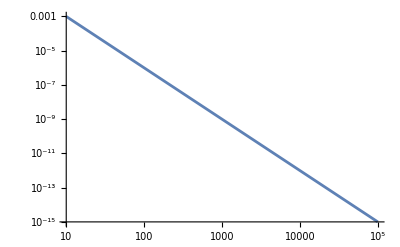

```mathematica
LogLogPlot[d^(-3),{d,10,100000}]
```

6.41732 r^(3/2)

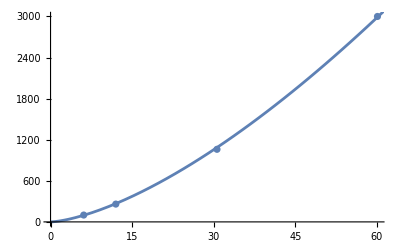

```mathematica
RvsT={{6.1,100},{12.,260},{30.6,1060},{60.1,3000}};
fofR[r_]=Fit[RvsT,{r^(3/2)},r]
Show[{ListPlot[RvsT],Plot[fofR[r],{r,0,75}]}]
```

```mathematica
{6.1/30.6,1071/101.}
```

{0.199346,10.604}

-682.5-190. e

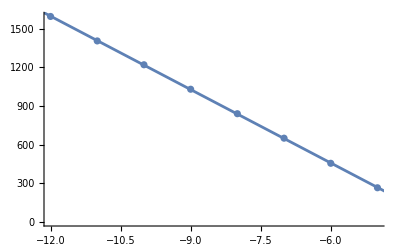

```mathematica
divTvsEps={{-5,265},{-6,455},{-7,650},{-8,840},{-9,1030},{-10,1220},{-11,1405},{-12,1595}};
TofE[e_]=Fit[divTvsEps,{1,e},e]
Show[{ListPlot[divTvsEps],Plot[TofE[e],{e,-13,-4}]}]
```

```mathematica
10.^(5/3)
```

46.4159

```mathematica
Series[mp ib^3 E^(I ib^(3/2)t),{ib,0,6}]
%/.t->{1/ib,1/ib^(3/2)}
```

mp ib^3+ⅈ mp t ib^(9/2)-1/2 (mp t^2) ib^6+O[ib]^7

{mp ib^3+ⅈ mp ib^(7/2)-(mp ib^4)/2+O[ib]^(15/2),(1/2+ⅈ) mp ib^3+O[ib]^8}

```mathematica
Sqrt[15./32/Pi]
```

0.386274

```mathematica
1./50^3
```

8.×10^-6

```mathematica
Pi/20.
```

0.15708

```mathematica
epsM[b_]=b^-3;
eps[mp_,b_]=mp/b^3;
```

```mathematica
{Sin[10^(-3./2)],Sin[100*100^(-3./2)],Sin[1000*1000^(-3./2)],Sin[10^(-5./2)],Sin[Pi/20.]}
eps[10^mpexp,10.^bexp]/.bexp->{5/3,2,3,4}/.mpexp->{0,-2,-3,-4,-5}//MatrixForm
epsM[10.^bexp]/.bexp->{5/3,2,3,4}//MatrixForm
10^texp*(10^bexp)^(-3./2)/.bexp->{5/3,2,3,4}/.texp->{1,2,3,4,5}//MatrixForm
Sin[10^texp*(10^bexp)^(-3./2)]/.bexp->{5/3,2,3,4}/.texp->{1,2,3,4,5}//MatrixForm
```

{0.0316175,0.0998334,0.0316175,0.00316227,0.156434}

(0.00001 | 1.×10^-7 | 1.×10^-8 | 1.×10^-9 | 1.×10^-10
1.×10^-6 | 1.×10^-8 | 1.×10^-9 | 1.×10^-10 | 1.×10^-11
1.×10^-9 | 1.×10^-11 | 1.×10^-12 | 1.×10^-13 | 1.×10^-14
1.×10^-12 | 1.×10^-14 | 1.×10^-15 | 1.×10^-16 | 1.×10^-17)

(0.00001
1.×10^-6
1.×10^-9
1.×10^-12)

(0.0316228 | 0.316228 | 3.16228 | 31.6228 | 316.228
0.01 | 0.1 | 1. | 10. | 100.
0.000316228 | 0.00316228 | 0.0316228 | 0.316228 | 3.16228
0.00001 | 0.0001 | 0.001 | 0.01 | 0.1)

(0.0316175 | 0.310984 | -0.0206835 | 0.205378 | 0.878681
0.00999983 | 0.0998334 | 0.841471 | -0.544021 | -0.506366
0.000316228 | 0.00316227 | 0.0316175 | 0.310984 | -0.0206835
0.00001 | 0.0001 | 0.001 | 0.00999983 | 0.0998334)

```mathematica
1/20.(*m/b*)
1/Sqrt[20.](*slow v*)
%/20(*omega*)
%*{1,5,10,15}
```

0.05

0.223607

0.0111803

{0.0111803,0.0559017,0.111803,0.167705}

```mathematica
Cos[7Pi/10]-Cos[7Pi/10+Pi/100.]
```

0.0251218

```mathematica
th0=Pi/3.;
ph0=1.;
Animate[Norm[SphericalHarmonicY[2,m,th0+dth,ph0+dph]-SphericalHarmonicY[2,m,th0,ph0]/.m->{-2,-1,0,1,2}],{dth,0,1/100.,1/1000},{dph,0,1/100,1/1000.}]
```

```mathematica
xh={1,0,0}
yh={0,1,0}
zh={0,0,1}
nh[thp_,php_]=Sin[thp](Cos[php]xh+Sin[php]yh)+Cos[thp]zh
ComplexExpand[FullSimplify[Norm[nh[Subscript[θ, p],Subscript[ϕ, p]]]],TargetFunctions->{Abs, Arg}]//Simplify
Eij[thp_,php_]=IdentityMatrix[3]-3Outer[Times,nh[thp,php],nh[thp,php]]
%//MatrixForm
%/.thp->Pi/2//MatrixForm
```

{1,0,0}

{0,1,0}

{0,0,1}

{Cos[php] Sin[thp],Sin[php] Sin[thp],Cos[thp]}

1

{{1-3 Cos[php]^2 Sin[thp]^2,-3 Cos[php] Sin[php] Sin[thp]^2,-3 Cos[php] Cos[thp] Sin[thp]},{-3 Cos[php] Sin[php] Sin[thp]^2,1-3 Sin[php]^2 Sin[thp]^2,-3 Cos[thp] Sin[php] Sin[thp]},{-3 Cos[php] Cos[thp] Sin[thp],-3 Cos[thp] Sin[php] Sin[thp],1-3 Cos[thp]^2}}

(1-3 Cos[php]^2 Sin[thp]^2 | -3 Cos[php] Sin[php] Sin[thp]^2 | -3 Cos[php] Cos[thp] Sin[thp]
-3 Cos[php] Sin[php] Sin[thp]^2 | 1-3 Sin[php]^2 Sin[thp]^2 | -3 Cos[thp] Sin[php] Sin[thp]
-3 Cos[php] Cos[thp] Sin[thp] | -3 Cos[thp] Sin[php] Sin[thp] | 1-3 Cos[thp]^2)

(1-3 Cos[php]^2 | -3 Cos[php] Sin[php] | 0
-3 Cos[php] Sin[php] | 1-3 Sin[php]^2 | 0
0 | 0 | 1)

```mathematica
Eij[thp,php][[1,1]]
```

1-3 Cos[php]^2 Sin[thp]^2

```mathematica
zsHarmonic[Eij_,thp_,php_]:={(-2(Eij[thp,php][[1,1]]-Eij[thp,php][[2,2]]))+I(-4Eij[thp,php][[1,2]]),
(-2Eij[thp,php][[1,3]])+I(-2Eij[thp,php][[2,3]]),
-2(Eij[thp,php][[1,1]]+Eij[thp,php][[2,2]]),
(-2Eij[thp,php][[1,3]])+I(2Eij[thp,php][[2,3]]),
(-2(Eij[thp,php][[1,1]]-Eij[thp,php][[2,2]]))+I(4Eij[thp,php][[1,2]])}
zs[Eij_,thp_,php_]:={Sqrt[4Pi/5](Eij[thp,php][[1,1]]-Eij[thp,php][[2,2]]+2I Eij[thp,php][[1,2]]),
2Sqrt[4Pi/5](Eij[thp,php][[1,3]]+I Eij[thp,php][[2,3]]),
-2Sqrt[6Pi/5](Eij[thp,php][[1,1]]+Eij[thp,php][[2,2]]),
-2Sqrt[4Pi/5](Eij[thp,php][[1,3]]-I Eij[thp,php][[2,3]]),
Sqrt[4Pi/5](Eij[thp,php][[1,1]]-Eij[thp,php][[2,2]]-2I Eij[thp,php][[1,2]])}
zs[Function[{v1,v2},m2/b^3Eij[v1,v2]],Pi/2,ωt]//Simplify
zs[m2/b^3Eij,thetap,phip]//MatrixForm
zs[Eij,thetap,phip]//Simplify//MatrixForm
%//TrigToExp//Simplify//MatrixForm
ComplexExpand[FullSimplify[Norm[zs[Eij,Subscript[θ, p],Subscript[ϕ, p]]]],TargetFunctions->{Abs, Arg}]//Simplify
Manipulate[{N[Norm[zs[Eij,θ,ϕ]]],Simplify[ComplexExpand[FullSimplify[Norm[zs[Eij,θ,ϕ]]],TargetFunctions->{Abs, Arg}]]},{θ,0,Pi,Pi/20},{ϕ,0,2Pi,Pi/20}]
Plot[Norm[zs[Eij,θ,0]],{θ,0,2Pi}]
```

{-(6 m2 √(π/5) (Cos[2 ωt]+ⅈ Sin[2 ωt]))/b^3,0,(2 m2 √((6 π)/5))/b^3,0,-(6 m2 √(π/5) (Cos[2 ωt]-ⅈ Sin[2 ωt]))/b^3}

Part::partd: Part specification (Eij m2)/b^3[thetap,phip]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification (Eij m2)/b^3[thetap,phip]⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification (Eij m2)/b^3[thetap,phip]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(2 √(π/5) ((Eij m2)/b^3[thetap,phip]⟦1,1⟧+2 ⅈ (Eij m2)/b^3[thetap,phip]⟦1,2⟧-(Eij m2)/b^3[thetap,phip]⟦2,2⟧)
4 √(π/5) ((Eij m2)/b^3[thetap,phip]⟦1,3⟧+ⅈ (Eij m2)/b^3[thetap,phip]⟦2,3⟧)
-2 √((6 π)/5) ((Eij m2)/b^3[thetap,phip]⟦1,1⟧+(Eij m2)/b^3[thetap,phip]⟦2,2⟧)
-4 √(π/5) ((Eij m2)/b^3[thetap,phip]⟦1,3⟧-ⅈ (Eij m2)/b^3[thetap,phip]⟦2,3⟧)
2 √(π/5) ((Eij m2)/b^3[thetap,phip]⟦1,1⟧-2 ⅈ (Eij m2)/b^3[thetap,phip]⟦1,2⟧-(Eij m2)/b^3[thetap,phip]⟦2,2⟧))

(-6 √(π/5) (Cos[2 phip]+ⅈ Sin[2 phip]) Sin[thetap]^2
-12 √(π/5) Cos[thetap] (Cos[phip]+ⅈ Sin[phip]) Sin[thetap]
-√((6 π)/5) (1+3 Cos[2 thetap])
12 √(π/5) Cos[thetap] (Cos[phip]-ⅈ Sin[phip]) Sin[thetap]
-6 √(π/5) (Cos[2 phip]-ⅈ Sin[2 phip]) Sin[thetap]^2)

(3/2 ⅇ^(2 ⅈ (phip-thetap)) (-1+ⅇ^(2 ⅈ thetap))^2 √(π/5)
3 ⅈ ⅇ^(ⅈ (phip-2 thetap)) (-1+ⅇ^(4 ⅈ thetap)) √(π/5)
-((1+3/2 (ⅇ^(-2 ⅈ thetap)+ⅇ^(2 ⅈ thetap))) √((6 π)/5))
-3 ⅈ ⅇ^(-ⅈ (phip+2 thetap)) (-1+ⅇ^(4 ⅈ thetap)) √(π/5)
3/2 ⅇ^(-2 ⅈ (phip+thetap)) (-1+ⅇ^(2 ⅈ thetap))^2 √(π/5))

4 √((6 π)/5) (Cos[1/2 Arg[(1+3 Cos[2 Conjugate[θ_p]]) (1+3 Cos[2 θ_p])+12 Cos[4 Re[ϕ_p]-4 ϕ_p] Sin[Conjugate[θ_p]]^2 Sin[θ_p]^2+12 Cosh[2 Im[ϕ_p]] Sin[2 Conjugate[θ_p]] Sin[2 θ_p]]]+ⅈ Sin[1/2 Arg[(1+3 Cos[2 Conjugate[θ_p]]) (1+3 Cos[2 θ_p])+12 Cos[4 Re[ϕ_p]-4 ϕ_p] Sin[Conjugate[θ_p]]^2 Sin[θ_p]^2+12 Cosh[2 Im[ϕ_p]] Sin[2 Conjugate[θ_p]] Sin[2 θ_p]]])

-Graphics-

### Extended Mass distributions

```mathematica
$Assumptions={R>2,R<10^6,0<=Costh^2<=zm<=1,ψ>=0,ψ<=2Pi,thp>=0,thp<=Pi}
```

{R>2,R<1000000,0≤Costh^2≤zm≤1,ψ≥0,ψ≤2 π,thp≥0,thp≤π}

```mathematica
ρpoint[r_,Costh_,ph_,M_,R_,z_,psi_]=M DiracDelta[r-R]DiracDelta[Costh-z]DiracDelta[ ph-psi];
ρpoint2[r_,th_,ph_,M_,R_,thp_,psi_]=M DiracDelta[r-R]DiracDelta[th-thp]DiracDelta[ ph-psi];
ρring[r_,ArcCosCosthoverzring_,ph_,Mring_,Rring_,zring_,psiring_]=Mring/(2Pi Rring) DiracDelta[r-Rring](DiracDelta[-ArcCosCosthoverzring+ph-psiring]+DiracDelta[+ArcCosCosthoverzring+ph-psiring]);
ρringshiftpihalf[r_,ArcSinCosthoverzring_,ph_,Mring_,Rring_,zring_,psiring_]=Mring/(Pi Rring) DiracDelta[r-Rring](DiracDelta[-ArcSinCosthoverzring+ph-psiring]+DiracDelta[+ArcSinCosthoverzring+ph-Pi-psiring]);
```

```mathematica
Integrate[ρring[r,ArcCosCosthoverzm,ph,Mring,R,zm,ψ],{ArcCosCosthoverzm,0,Pi}]
Integrate[ρring[r,ArcCosCosthoverzm,ph,Mring,R,zm,ψ]r,{r,0,Infinity},{ArcCosCosthoverzm,0,Pi},{ph,ψ-Pi,Pi+ψ}]
Integrate[ρringshiftpihalf[r,ArcSinCosthoverzm,ph,Mring,R,zm,ψ]r,{r,0,Infinity},{ArcSinCosthoverzm,-Pi/2,Pi/2},{ph,ψ-Pi/2,ψ+Pi/2}]
```

(Mring DiracDelta[r-R] HeavisideTheta[ph-ψ,-ph+π+ψ])/(2 π R)+(Mring DiracDelta[r-R] HeavisideTheta[ph+π-ψ,-ph+ψ])/(2 π R)

Mring

Mring

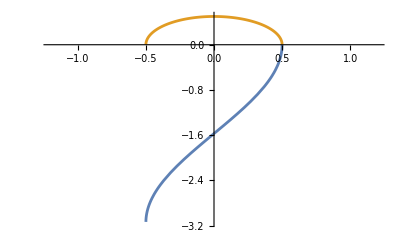

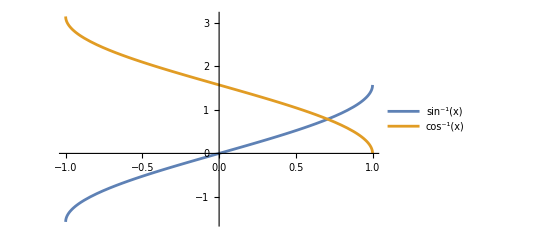

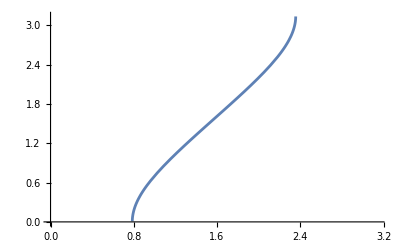

```mathematica
Plot[{-Pi/2+ArcSin[2x],1/D[-Pi/2+ArcSin[2y],y]/.y->x},{x,-1.2,1.2}]
Plot[{ArcSin[x],ArcCos[x]},{x,-1,1},PlotLegends->"Expressions"]
Plot[ArcCos[Cos[x]/Cos[Pi/4]],{x,0,Pi}]
```

0

Abs[1/(√(1-y^2/z^2) z)]

Abs[√(1-y^2/z^2) z]

Abs[√(1-y^2/z^2) z]

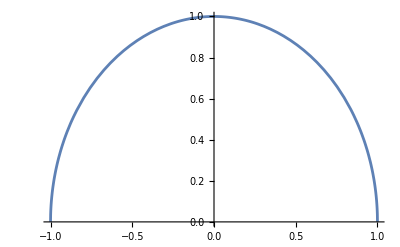

```mathematica
-π+2 ArcSin[2 Costh]/.Costh->1/2
Abs[D[ph-ArcSin[y/z]-ψ,y]]//FullSimplify
1/%//FullSimplify
%/.ph->{0,Pi/3,Pi/2}
Plot[√Abs[1^2-y^2] ,{y,-1,1}]
```

```mathematica
2 Abs[1/(√(z^2-y^2))]
```

2/(√Abs[-y^2+z^2])

```mathematica
1/2 √Abs[z^2-y^2]
```

1/2 √Abs[-y^2+z^2]

```mathematica
Solve[Costh==zring Sin[ϕ-ψ],ϕ](*Sets the Ascending Node(inersection with equatorial plane, assuming prograde accretion disc) at phi=0+ψ*)
Solve[Costh==zring Cos[ϕ-ψ],ϕ](*Sets the Ascending Node at phi=-pi/2+ψ*)
Solve[ArcCos[Costh/zring]==ϕ-ψ,Costh]
```

{{ϕ→ConditionalExpression[π+ψ-ArcSin[Costh/zring]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ψ+ArcSin[Costh/zring]+2 π C[1], C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[ψ-ArcCos[Costh/zring]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ψ+ArcCos[Costh/zring]+2 π C[1], C[1]∈ℤ]}}

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[ArcCos[Costh/zring]==ϕ-ψ,Costh]

```mathematica
NewEij[thp_,ψ_]:=Integrate[ ρpoint2[r,th,ph,Mring,R,thp,ψ]/ r^3Eij[th,ph],{r,0,Infinity},{th,0,Pi},{ph,0,2Pi}]
zs[NewEij,thp,ψ]/.thp->Pi/2//Simplify
(*Plot[Norm[%],{θ,0,2Pi}]*)
```

{-(6 Mring √(π/5) (Cos[2 ψ]+ⅈ Sin[2 ψ]))/R^3,0,(2 Mring √((6 π)/5))/R^3,0,-(6 Mring √(π/5) (Cos[2 ψ]-ⅈ Sin[2 ψ]))/R^3}

```mathematica
Integrate[#/ r^3Eij[ArcCos[Costh],ph]r,{r,0,Infinity},{Costh,-1,1},{ph,0,2Pi}]&/@{ρpoint[r,Costh,ph,Mp,R,0,Pi/2],ρring[r,Costh,ph,Mring,R,0,0]}
```

{{{Mp/R^2,0,0},{0,-(2 Mp)/R^2,0},{0,0,Mp/R^2}},{{(3 Mring (2 Cos[2]-Sin[2]))/(8 π R^3),(3 Mring (-3+Cos[2]+2 Sin[2]))/(8 π R^3),0},{(3 Mring (-3+Cos[2]+2 Sin[2]))/(8 π R^3),(3 Mring (-2 Cos[2]+Sin[2]))/(8 π R^3),0},{0,0,0}}}

```mathematica
Integrate[DiracDelta[th-thp],{th,0,Pi},Assumptions->{thp>=0,thp<=Pi}]
Integrate[DiracDelta[Cos[th]-Cos[thp]],{th,0,Pi},Assumptions->{thp>=0,thp<=Pi}]
Integrate[DiracDelta[Cos[th]-zm],{th,0,Pi},Assumptions->{zm>=-1,zm<=1}]
Integrate[DiracDelta[Cos[th]-1/2],{th,0,Pi},Assumptions->{zm>=-1,zm<=1}]
```

HeavisideTheta[π-thp] HeavisideTheta[thp]

Integrate[DiracDelta[Cos[th]-Cos[thp]],{th,0,π},Assumptions→{thp≥0,thp≤π}]

Integrate[DiracDelta[-zm+Cos[th]],{th,0,π},Assumptions→{zm≥-1,zm≤1}]

2/(√3)

```mathematica
GenEij[ρ_][thp_,ψ_]:=Integrate[ ρ/ r^3Eij[ArcCos[Costh],ph],{r,0,Infinity},{Costh,-1,1},{ph,0,2Pi}]
RingEij[thp_,ψ_]:=Integrate[ρring[r,χ,ph,Mring,R,Cos[thp],ψ]/ r^3Eij[ArcCos[Cos[thp] Cos[χ]],ph] r,{r,0,Infinity},{χ,0,Pi},{ph,ψ-Pi,Pi+ψ}]
RingEijshiftpihalf[thp_,ψ_]:=Integrate[ρringshiftpihalf[r,χ,ph,Mring,R,Cos[thp],ψ]/ r^3Eij[ArcCos[Cos[thp] Sin[χ]],ph] r,{r,0,Infinity},{χ,-Pi/2,Pi/2},{ph,ψ-Pi/2,ψ+Pi/2}]
```

```mathematica
(*zs[GenEij[ρ[r,Costh,ph,Mring,R,zm,ψ]],ArcCos[zm],ψ]/.ρ->ρpoint(*,ρring}*)//Simplify//TrigToExp//Simplify//MatrixForm
Simplify[zs[RingEij,ArcCos[zm],ψ]/EllipticK[zm^2]/EllipticE[zm^2]//TrigToExp,TransformationFunctions->{EllipticK,EllipticE,Automatic}];
%*EllipticK[zm^2]*EllipticE[zm^2]//Simplify//MatrixForm
Simplify[zs[RingEijshiftpihalf,ArcCos[zm],ψ]/EllipticK[zm^2]/EllipticE[zm^2]//TrigToExp,TransformationFunctions->{EllipticK,EllipticE,Automatic}];
%*EllipticK[zm^2]*EllipticE[zm^2]//Simplify//MatrixForm*)
```

```mathematica
Cos[Pi/2-ArcCos[zm]]//TrigReduce
```

√(1-zm^2)

```mathematica
Simplify[{Sqrt[zm^2],Surd[zm^2,2]},1>zm>0]
```

{zm,zm}

```mathematica
{# Pi/10}&/@Range[1,4]//N
```

{{0.314159},{0.628319},{0.942478},{1.25664}}

```mathematica
zPoint=({{(6 ⅇ^(2 ⅈ ψ) Mring √(π/5) (-1+zm^2))/R^3}, {-(12 ⅇ^(ⅈ ψ) Mring √(π/5) zm √(1-zm^2))/R^3}, {-(2 Mring √((6 π)/5) (-1+3 zm^2))/R^3}, {(12 ⅇ^(-ⅈ ψ) Mring √(π/5) zm √(1-zm^2))/R^3}, {(6 ⅇ^(-2 ⅈ ψ) Mring √(π/5) (-1+zm^2))/R^3}})
(zPoint/.{zm->-zm,ψ->ψ+Pi})-zPoint//Simplify
Simplify[(zPoint/.{zm->√(1-zm^2),ψ->ψ+Pi})+zPoint-((zPoint/.{zm->√(1-zm^2)})+(zPoint/.{ψ->ψ+Pi})),1>zm>0]
Simplify[(zPoint/.{zm->√(1-zm1^2),ψ->ψ+Pi})+(zPoint/.{zm->zm1})-((zPoint/.{zm->√(1-zm2^2)})+(zPoint/.{zm->zm2,ψ->ψ+Pi})),1>=zm1>=0 &&1>=zm2>=0]
Simplify[(zPoint/.{zm->√(1-zm^2),ψ->ψ+Pi})+zPoint-((zPoint/.{zm->√(1-zm2^2),ψ->ψ+Pi})+(zPoint/.{zm->zm2})),1>=zm>=0 &&1>=zm2>=0]
```

{(6 ⅇ^(2 ⅈ ψ) Mring √(π/5) (-1+zm^2))/R^3,-(12 ⅇ^(ⅈ ψ) Mring √(π/5) zm √(1-zm^2))/R^3,-(2 Mring √((6 π)/5) (-1+3 zm^2))/R^3,(12 ⅇ^(-ⅈ ψ) Mring √(π/5) zm √(1-zm^2))/R^3,(6 ⅇ^(-2 ⅈ ψ) Mring √(π/5) (-1+zm^2))/R^3}

{0,0,0,0,0}

{0,0,0,0,0}

{0,0,0,0,0}

«1 more identical outputs»

```mathematica
zRing=({{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}, {-(8 ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {(Mring √((6 π)/5) (2-3 zm^2))/R^3}, {(8 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}})
(zRing/.{zm->-zm,ψ->ψ+Pi})-zRing//Simplify
(zRing/.{ψ->ψ+Pi})-zRing//Simplify
```

{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3),-(8 ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),(Mring √((6 π)/5) (2-3 zm^2))/R^3,(8 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}

{0,0,0,0,0}

{0,(16 ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),0,-(16 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),0}

```mathematica
Limit[(8 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),zm->0]
Limit[(8 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),zm->1]
Limit[(8 ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm),zm->-1]
```

0

(8 ⅇ^(-ⅈ ψ) Mring)/(√(5 π) R^3)

-(8 ⅇ^(-ⅈ ψ) Mring)/(√(5 π) R^3)

```mathematica
TeXForm[MatrixForm[zPoint]]
```

\left(
\begin{array}{c}
 \frac{6 \sqrt{\frac{\pi }{5}} \text{Mring} e^{2 i \psi }
   \left(\text{zm}^2-1\right)}{R^3} \\
 -\frac{12 \sqrt{\frac{\pi }{5}} \text{Mring} e^{i \psi } \text{zm}
   \sqrt{1-\text{zm}^2}}{R^3} \\
 -\frac{2 \sqrt{\frac{6 \pi }{5}} \text{Mring} \left(3
   \text{zm}^2-1\right)}{R^3} \\
 \frac{12 \sqrt{\frac{\pi }{5}} \text{Mring} e^{-i \psi } \text{zm}
   \sqrt{1-\text{zm}^2}}{R^3} \\
 \frac{6 \sqrt{\frac{\pi }{5}} \text{Mring} e^{-2 i \psi }
   \left(\text{zm}^2-1\right)}{R^3} \\
\end{array}
\right)

```mathematica
TeXForm[MatrixForm[zRing]]
```

\left(
\begin{array}{c}
 \frac{3 \sqrt{\frac{\pi }{5}} \text{Mring} e^{2 i \psi } \text{zm}^2}{2 R^3}
   \\
 -\frac{8 \text{Mring} e^{i \psi } \left(\left(2 \text{zm}^2-1\right)
   E\left(\text{zm}^2\right)-\left(\text{zm}^2-1\right)
   K\left(\text{zm}^2\right)\right)}{\sqrt{5 \pi } R^3 \text{zm}} \\
 \frac{\sqrt{\frac{6 \pi }{5}} \text{Mring} \left(2-3 \text{zm}^2\right)}{R^3}
   \\
 \frac{8 \text{Mring} e^{-i \psi } \left(\left(2 \text{zm}^2-1\right)
   E\left(\text{zm}^2\right)-\left(\text{zm}^2-1\right)
   K\left(\text{zm}^2\right)\right)}{\sqrt{5 \pi } R^3 \text{zm}} \\
 \frac{3 \sqrt{\frac{\pi }{5}} \text{Mring} e^{-2 i \psi } \text{zm}^2}{2 R^3}
   \\
\end{array}
\right)

```mathematica
zRingRotated=({{-(3 ⅇ^(2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}, {-(8 ⅈ ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {(Mring √((6 π)/5) (2-3 zm^2))/R^3}, {-(8 ⅈ ⅇ^(-ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {-(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}})
```

```mathematica
Exp[I Pi/2]
Exp[I Pi]
```

ⅈ

-1

```mathematica
ComplexExpand[Simplify[Norm[Normal[({{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}, {-(8 ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {-(Mring √((6 π)/5) (-2+3 zm^2))/R^3}, {(8 ⅇ^(ⅈ ψ) Mring ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]))/(√(5 π) R^3 zm)}, {(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5) zm^2)/(2 R^3)}})]]],TargetFunctions->{Abs, Arg}]//Simplify
```

```mathematica
Limit[(√((Mring^2 (3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 Abs[(-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]]^2))/(R^6 zm^2)))/(√(10 π)),zm->0]
Limit[(√((Mring^2 (3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 Abs[(-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]]^2))/(R^6 zm^2)))/(√(10 π)),zm->1]
```

2 √((6 π)/5) √(Mring^2/R^6)

$Aborted

```mathematica
EllipticK[1]
```

ComplexInfinity

```mathematica
Series[(-1+zm^2) EllipticK[zm^2],{zm,1,7}]
Limit[%,zm->1]
Series[(-1+2 zm^2) EllipticE[zm^2],{zm,1,7}]
Limit[%,zm->1]
```

Piecewise[{{∞ (zm-1)+∞ (zm-1)^2+O[zm-1]^8, zm==1}, {(3 Log[2]-Log[1-zm]) (zm-1)+1/2 (zm-1)^2+1/16 (-3+3 Log[2]-Log[1-zm]) (zm-1)^3+1/96 (13-18 Log[2]+6 Log[1-zm]) (zm-1)^4+((-229+342 Log[2]-114 Log[1-zm]) (zm-1)^5)/2048+((2957-4500 Log[2]+1500 Log[1-zm]) (zm-1)^6)/30720+((-8317+12690 Log[2]-4230 Log[1-zm]) (zm-1)^7)/98304+O[zm-1]^8, True}}]

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

$Failed+4 $Failed (zm-1)+2 $Failed (zm-1)^2+O[zm-1]^8

$Failed

```mathematica
(√((Mring^2 (3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 Abs[(-1+2 zm^2) EllipticE[zm^2]]^2))/(R^6 zm^2)))/(√(10 π))/.zm->1//Simplify
```

√(1/10 (256/π+21 π)) √(Mring^2/R^6)

```mathematica
(1/8+1/6)/2
```

7/48

(√((3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2])^2)/zm^2))/(√(10 π))

{4.01053,{th→0.46276}}

4.01053

0.46276

0.458149

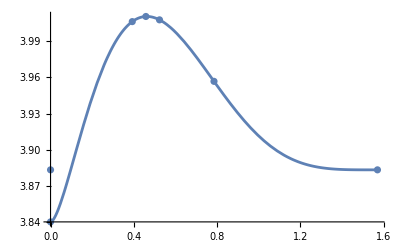

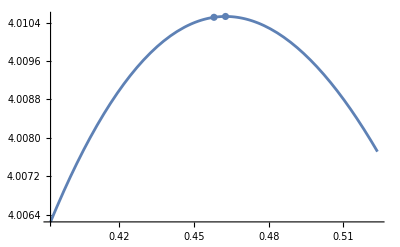

```mathematica
f[zm_]=(√((3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2])^2)/zm^2))/(√(10 π))
FindMaximum[f[Cos[th]],{th,Pi/8}]
ymax=First[%]
xmax=th/.Last[%%]
N[7Pi/48]
(*FindInstance[Evaluate[D[f[Cos[th]],th]]==0,th,Reals]*)
Show[Plot[f[Cos[th]],{th,0,Pi/2}],ListPlot[{{0,√(1/10 (256/π+21 π))},{0,2 √((6 π)/5)},{Pi/8,f[Cos[Pi/8]]},{7Pi/48,f[Cos[7Pi/48]]},{Pi/6,f[Cos[Pi/6]]},{Pi/4,√(((21 π^2)/8+64 EllipticK[1/2]^2)/(5 π))},{Pi/2,2 √((6 π)/5)}}]]
Show[Plot[f[Cos[th]],{th,Pi/8,Pi/6}],ListPlot[{{7Pi/48,f[Cos[7Pi/48]]},{xmax,ymax}}]]
```

```mathematica
π/4
```

```mathematica
Abs[(-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]]^2/.zm->0//Simplify
Abs[(-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2]]^2/.zm->1//Simplify
```

0

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

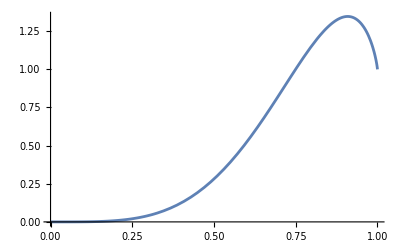

```mathematica
Plot[((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2])^2,{zm,0,1}]
```

```mathematica
TeXForm[√((3 π^2 zm^2 (16-48 zm^2+39 zm^4)+256 ((-1+2 zm^2) EllipticE[zm^2]-(-1+zm^2) EllipticK[zm^2])^2)/(10 π zm^2))]
```

\frac{\sqrt{\frac{256 \left(\left(2 \text{zm}^2-1\right)
   E\left(\text{zm}^2\right)-\left(\text{zm}^2-1\right)
   K\left(\text{zm}^2\right)\right)^2+3 \pi ^2 \left(39 \text{zm}^4-48
   \text{zm}^2+16\right) \text{zm}^2}{\text{zm}^2}}}{\sqrt{10 \pi }}

```mathematica
ρpolarring[r_,ph_,Mring_,Rring_,psiring_]=Mring/(2Pi Rring) DiracDelta[r-Rring](DiracDelta[ph-psiring+Pi/2](*+DiracDelta[ph-psiring-Pi]*));
Integrate[ρpolarring[r,ph,Mring,R,ψ]r,{r,0,Infinity},{th,0,2Pi},{ph,ψ-Pi,Pi+ψ}]
```

Mring

```mathematica
PolarRingEij[thp_,ψ_]:=Integrate[ρpolarring[r,ph,Mring,R,ψ]/ r^3Eij[th,ph] r,{r,0,Infinity},{th,0,2Pi},{ph,ψ-Pi,Pi+ψ}]
Simplify[zs[PolarRingEij,0,ψ]]//TrigToExp
```

{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5))/R^3,0,-(Mring √((6 π)/5))/R^3,0,(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5))/R^3}

```mathematica
ComplexExpand[Norm[{3 √(π/5) (Cos[2 ψ]+ⅈ Sin[2 ψ]),0,-√((6 π)/5),0,3  √(π/5) (Cos[2 ψ]-ⅈ Sin[2 ψ])}],TargetFunctions->{Abs, Arg}]//FullSimplify
```

2 √((6 π)/5)

```mathematica
Limit[zRing,zm->1]//Simplify
Limit[zRing,zm->-1]//Simplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5))/(2 R^3),-(8 ⅇ^(ⅈ ψ) Mring)/(√(5 π) R^3),-(Mring √((6 π)/5))/R^3,(8 ⅇ^(-ⅈ ψ) Mring)/(√(5 π) R^3),(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5))/(2 R^3)}

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{(3 ⅇ^(2 ⅈ ψ) Mring √(π/5))/(2 R^3),(8 ⅇ^(ⅈ ψ) Mring)/(√(5 π) R^3),-(Mring √((6 π)/5))/R^3,-(8 ⅇ^(-ⅈ ψ) Mring)/(√(5 π) R^3),(3 ⅇ^(-2 ⅈ ψ) Mring √(π/5))/(2 R^3)}

```mathematica
ComplexExpand[Norm[{(3 ⅇ^(2 ⅈ ψ) √(π/5))/2,(8 ⅇ^(ⅈ ψ))/(√(5 π)),- √((6 π)/5),-(8 ⅇ^(-ⅈ ψ))/(√(5 π)),(3 ⅇ^(-2 ⅈ ψ)  √(π/5))/2}],TargetFunctions->{Abs, Arg}]//FullSimplify
```

√(128/(5 π)+(21 π)/10)

```mathematica
N[{2 √((6 π)/5),√(128/(5 π)+(21 π)/10)}]
```

{3.88325,3.84006}

```mathematica
ρequatring[r_,th_,Mring_,Rring_]=Mring/(2Pi Rring) DiracDelta[r-Rring]DiracDelta[th-Pi/2];
Integrate[ρequatring[r,th,Mring,R]r,{r,0,Infinity},{th,0,Pi},{ph,0,2Pi}]
```

Mring

```mathematica
EquatRingEij[thp_,ψ_]:=Integrate[ρequatring[r,th,Mring,R]/ r^3Eij[th,ph] r,{r,0,Infinity},{th,0,Pi},{ph,0,2Pi}]
Simplify[zs[EquatRingEij,Pi/2,ψ]]//TrigToExp
```

{0,0,(2 Mring √((6 π)/5))/R^3,0,0}